```mathematica
r[t_]:=ρ{Cos[ω0 t],Sin[ω0 t],0}
n[θ_]:={Sin[θ],0,Cos[θ]}
β[t_]:=ρ*ω0{-Sin[ω0 t],Cos[ω0 t],0}
tripleproduct[t_,θ_]:=Cross[n[θ],Cross[n[θ],β[t]/c]]
int[t_,θ_,ω_]:=tripleproduct[t,θ]*Exp[I ω (t-Dot[n[θ],r[t]]/c)]
intre[t_,θ_]:=cp[t,θ]*Cos[ ω (t-Dot[n[θ],r[t]]/c)]
intim[t_,θ_]:=cp[t,θ]*Sin[ ω (t-Dot[n[θ],r[t]]/c)]
ρ=100;
b=.9;
c=3*10^8;
ω0=(b c)/ρ;
T=(2Pi)/ω0//N
```

2.32711×10^-6

```mathematica
tripleproduct[1,2]
```

{0.128162,0.512162,0.28004}

```mathematica
Clear["Global`*"]
```

```mathematica
f[θ_,ω_]:=ω^2/4((Norm[NIntegrate[int[t,θ,ω],{t,-T/2,T/2}]])^2)
```

```mathematica
γ=Sqrt[1-b^2]^-1;
ξ[θ_,ω_]:=(ω ρ)/(3 c)(γ^-2+θ^2)^(3/2);
intensity[θ_]:=1/3((ω ρ)/c)^2(γ^-2+θ^2)^2((BesselK[2/3,ξ[θ]])^2+θ^2/(γ^-2+θ^2)(BesselK[1/3,ξ[θ]])^2)
```

```mathematica
Clear[all]
```

```mathematica
Jackson1[θ_,ω_]:=ω^2/(4 π^2)((Norm[NIntegrate[int[t,θ,ω],{t,-T/2,T/2}]])^2)
Jackson2[θ_,ω_]:=1/(3 π^2)((ω ρ)/c)^2(γ^-2+θ^2)^2((BesselK[2/3,ξ[θ,ω]])^2+θ^2/(γ^-2+θ^2)(BesselK[1/3,ξ[θ,ω]])^2)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

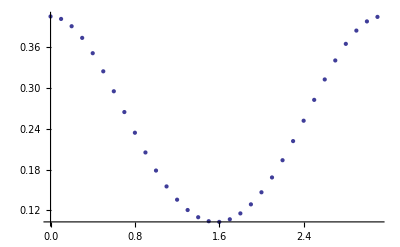

```mathematica
ListPlot[Table[{θ,Jackson1[θ,1*ω0]},{θ,0,π,.1}]]
```

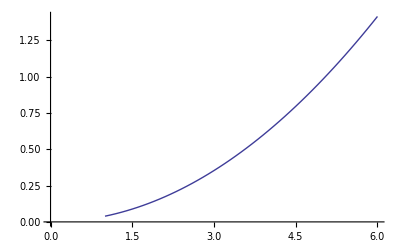

```mathematica
ListLinePlot[Table[{θ,Jackson3[1,ω0*θ]},{θ,1,6,.1}]]
```

```mathematica
Jackson2[1,2*ω0]
```

0.126876

```mathematica
p31 = ListPlot[Table[{θ,Jackson2[θ-π/2.,ω0*4]},{θ,0,π,.1}],AxesLabel->{θ,"Intensity"},PlotLegends->Automatic];
```

```mathematica
p32 = ListPlot[Table[{θ,Jackson1[θ,ω0*4]},{θ,0,π,.1}],AxesLabel->{θ,"Intensity"},PlotLegends->Automatic];
```

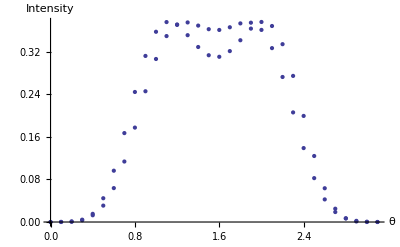

```mathematica
Show[p31,p32]
```

```mathematica
ListDensityPlot[ArrayFlatten[Table[{θ,n,Log[Abs[Jackson1[θ,ω0*n]-Jackson2[θ-π/2.,ω0*n]]]},{n,1,10,.5},{θ,0,π,.1}],1],AxesLabel->{θ,n,"Intensity"},PlotLegends->Automatic]
```

NIntegrate::inumr: The integrand ⅇ^(0.  + 2.7×10^6\ ⅈ)\ (t - 1.[0.] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1.[0.] × (1.[0.] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0.}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

NIntegrate::inumr: The integrand ⅇ^(0.  + 2.7×10^6\ ⅈ)\ (t - 1.[0.1] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1.[0.1] × (1.[0.1] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0.}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-7.81798×10^-7}. NIntegrate obtained 4.63221×10^-23 + 4.63221×10^-23\ ⅈ and 2.21002×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-1.1635528344599304083267073223136820444657750055623410468568293408×10^-6}. NIntegrate obtained -2.8455×10^-22 - 1.32349×10^-23\ ⅈ and 6.85779×10^-22 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-6.27264×10^-7}. NIntegrate obtained -5.12852×10^-23 + 4.96308×10^-24\ ⅈ and 2.2451×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

-Graphics-

```mathematica
(*This is the error plot to compare the exact jackson result to the approx jackson result. I took the log10, so this will show the magnitude of the error between them. Note, that for some regions, the magnitude of the error is larger than 10^0, which means that for some regions, the approximate result is very poor. Note, for small ω, and angles close to π/2, we have very good agreement between the exact jackson, and the approximate jackson.*)
```

```mathematica
newint[t_,θ_,ω_]:=Cross[n[θ],β[t]]Exp[I ω (t-Dot[n[θ],r[t]]/c)]
Jackson3[θ_,ω_]:=ω^2/(4 π^2)((Norm[NIntegrate[newint[t,θ,ω],{t,-T/2,T/2}]])^2)
```

```mathematica
ListPlot3D[ArrayFlatten[Table[{θ,n,Jackson1[θ,ω0*n]-Jackson3[θ,ω0*n]},{n,1,10},{θ,0,π,.1}],1],AxesLabel->Automatic]
```

NIntegrate::inumr: The integrand ⅇ^10000000\ ⅈ\ (t - 1[0.] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1[0.] × (1[0.] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

NIntegrate::inumr: The integrand ⅇ^10000000\ ⅈ\ (t - 1[0.] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1[0.] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0} has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

-Graphics3D-

```mathematica
(*Looking at the scale of this graph, we can see that an error of 10^-15, is probably numerical in origin, and the two results agree very well. Jackson1 uses B^2, Jackson3 uses E^2 (n cross B)
```

```mathematica
besselp[n_,y_]:=D[BesselJ[n,x],x]/.x->y
Landau[θ_,n_]:=n^2(Tan[θ]^2 BesselJ[n,b n Cos[θ]]^2+b^2(1/2 (BesselJ[-1+n,b n Cos[θ]]-BesselJ[1+n,b n Cos[θ]]))^2)
```

```mathematica
Landau[1-π/2,3]
```

0.343947

```mathematica
Jackson3[1,3*ω0]
```

3.18068×10^16

```mathematica
D[BesselJ[n,x],x]
```

1/2 (BesselJ[-1+n,x]-BesselJ[1+n,x])

```mathematica
DataLandau =Table[{n,θ,Log10[Abs[Jackson1[θ,ω0*n]-Landau[θ-π/2,n]]]},{n,1,10,.2},{θ,0,π,.5}]
```

NIntegrate::inumr: The integrand ⅇ^(0.  + 2.7×10^6\ ⅈ)\ (t - 1.[0.] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1.[0.] × (1.[0.] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0.}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-7.81798×10^-7}. NIntegrate obtained 4.63221×10^-23 + 4.63221×10^-23\ ⅈ and 2.21002×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-1.1635528344599304083267073223136820444657750055623410468568293408×10^-6}. NIntegrate obtained -2.8455×10^-22 - 1.32349×10^-23\ ⅈ and 6.85779×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-6.27264×10^-7}. NIntegrate obtained -5.12852×10^-23 + 4.96308×10^-24\ ⅈ and 2.2451×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
ListDensityPlot[ArrayFlatten[DataLandau,1],PlotLegends->Automatic,AxesLabel->"n"]
```

-Graphics-

```mathematica
(*They both seem to agree very well when they have integer values. As you move away from integer values, the agreement becomes very poor. I am plotting the Log10 of the difference between the jackson exact, and the landau formula*)
```

```mathematica
DataLandau2 ={ListDensityPlot[ArrayFlatten[Table[{n,θ,Landau[θ-π/2,n]},{n,1,10,.2},{θ,0,π,.1}],1],PlotLegends->Automatic],ListDensityPlot[ArrayFlatten[Table[{n,θ,Jackson1[θ,ω0*n]},{n,1,10,.2},{θ,0,π,.1}],1],PlotLegends->Automatic]}
```

NIntegrate::inumr: The integrand ⅇ^(0.  + 2.7×10^6\ ⅈ)\ (t - 1.[0.] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1.[0.] × (1.[0.] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0.}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

NIntegrate::inumr: The integrand ⅇ^(0.  + 2.7×10^6\ ⅈ)\ (t - 1.[0.1] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1.[0.1] × (1.[0.1] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0.}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

NIntegrate::inumr: The integrand ⅇ^(0.  + 2.7×10^6\ ⅈ)\ (t - 1.[0.2] . {Times[« 2 »], Times[« 2 »], 0}/300000000)\ 1.[0.2] × (1.[0.2] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0.}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-7.81798×10^-7}. NIntegrate obtained 4.63221×10^-23 + 4.63221×10^-23\ ⅈ and 2.21002×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-1.1635528344599304083267073223136820444657750055623410468568293408×10^-6}. NIntegrate obtained -2.8455×10^-22 - 1.32349×10^-23\ ⅈ and 6.85779×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-6.27264×10^-7}. NIntegrate obtained -5.12852×10^-23 + 4.96308×10^-24\ ⅈ and 2.2451×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
p2=ListPlot[Table[{θ,Jackson1[θ,4*ω0]},{θ,0,π,.1}]];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
Landau[.4,10]
```

0.38144

```mathematica
Jackson1[.4,10*ω0]
```

0.975528

```mathematica
p2l=ListPlot[Table[{θ,Landau[θ-π/2,4]},{θ,0,π,.1}],PlotStyle->Red];
```

```mathematica
DataLandau2 =Show[p2,p2l]
```

-Graphics-

```mathematica
ArrayFlatten[DataLandau,1]
```

```mathematica
ListDensityPlot[ArrayFlatten[DataLandau,1]]
```

$Aborted

```mathematica
ContourPlot[Log[Jackson1[θ,ω]-Landau[θ-π/2,ω/ω0]],{θ,0,Pi},{ω,0,10*ω0},PlotLegends->Automatic]
```

$Aborted

```mathematica
Plot3D[Jackson1[θ-π/2,n],{θ,0,Pi},{n,0,30}]
```

NIntegrate::inumr: The integrand ⅇ^10000000\ ⅈ\ (t - 0.002145[-1.57057] . {« 1 »}/300000000)\ 0.002145[-1.57057] × (0.002145[-1.57057] × {-0.9\ Sin[2.7×10^6\ t], 0.9\ Cos[2.7×10^6\ t], 0}) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.16355×10^-6, 1.16355×10^-6}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

$Aborted

```mathematica
Landau[2.5,10]
```

-2.37423

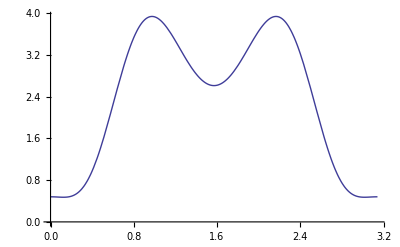

```mathematica
Plot[Jackson1[θ,10*ω0],{θ,0,Pi}]
```